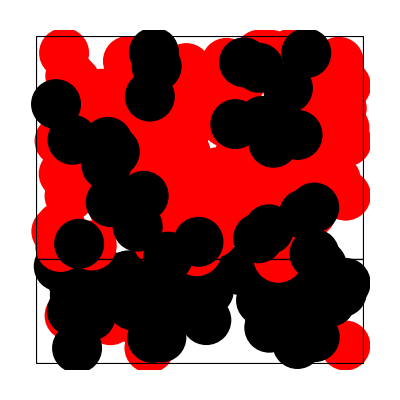

```mathematica
Graphics[{
PointSize[0.09],
Riffle[

{Table[{Red,Point[{RandomReal[{0,1}],RandomReal[{0,0.3}]}]},{0.3*0.15*200}],
Table[{Red,Point[{RandomReal[{0,1}],RandomReal[{0.3,1}]}]},{0.7*0.8*200}]},

{Table[Point[{RandomReal[{0,1}],RandomReal[{0,0.3}]}],{0.3*0.85*200}],
Table[Point[{RandomReal[{0,1}],RandomReal[{0.3,1}]}],{0.7*0.2*200}]}
],
{EdgeForm[Thick],FaceForm[None],Rectangle[{-0.05,-0.05},{1.05,1.05}]},
{Thick,Line[{{-0.05,0.3},{1.05,0.3}}]}
}]
```

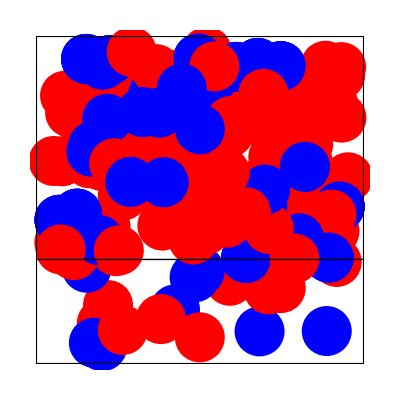

```mathematica
Graphics[{
PointSize[0.09],
Riffle[
Table[{Red,Point[{RandomReal[{0,1}],RandomReal[{0,0.3}]}]},{0.3*0.15*200}],
Table[{Blue,Point[{RandomReal[{0,1}],RandomReal[{0,0.3}]}]},{0.3*0.85*200}]
],
Riffle[
Table[{Red,Point[{RandomReal[{0,1}],RandomReal[{0.3,1}]}]},{0.7*0.8*200}],
Table[{Blue,Point[{RandomReal[{0,1}],RandomReal[{0.3,1}]}]},{0.7*0.2*200}]
],
{EdgeForm[Thick],FaceForm[None],Rectangle[{-0.05,-0.05},{1.05,1.05}]},
{Thick,Line[{{-0.05,0.3},{1.05,0.3}}]}
}]
```